# Omicron analysis: Plotting partitioned case counts and Rt

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/trvrb/Documents/src/rt-from-frequency-dynamics/results/omicron-countries

```mathematica
dataset="omicron-countries";
```

## Setup

### Variants

```mathematica
variants={"other","Delta","Omicron"};
```

```mathematica
n=Length[variants]
```

3

### Colors

```mathematica
colors=Prepend[Table[ColorData["Rainbow"][i],{i,{0.3,0.95}}],Gray]
```

{GrayLevel[0.5],RGBColor[0.2979596, 0.5657928, 0.7522386000000001],RGBColor[0.8739574, 0.2607876000000001, 0.15481040000000004]}

### Date ticks

```mathematica
dateTicks={"2021-09-01","2021-10-01","2021-11-01","2021-12-01"};
```

### Smoothing functions

```mathematica
smoothed[dateSeries_]:=Map[{#[[4,1]],N[Mean[#[[All,2]]]]}&,Partition[dateSeries,7,1]]
```

```mathematica
simplePrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[1]],N[(#1[[2]])/(0.0001+#2[[2]])]}&,{dateSeriesPositives,dateSeriesTotals}]
```

```mathematica
smoothedPrevalence[dateSeriesPositives_,dateSeriesTotals_]:=MapThread[{#1[[4,1]],N[Total[#1[[All,2]]]/(0.0001+Total[#2[[All,2]]])]}&,{Partition[dateSeriesPositives,7,1],Partition[dateSeriesTotals,7,1]}]
```

```mathematica
gappedPartition[list_,n_]:=Partition[list,n,n,1,""]
```

## Sequence counts

```mathematica
seqData=Import["../../data/"<>dataset<>"_location-variant-sequence-counts.tsv","TSV"];
```

```mathematica
header=seqData[[1]]
```

{date,location,variant,sequences}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,variant→3,sequences→4}

```mathematica
seqData=Drop[seqData,1];
```

```mathematica
startDate=First[Sort[Union[seqData[[All,1]]]]]
```

2021-09-01

```mathematica
endDate=Last[Sort[Union[seqData[[All,1]]]]]
```

2021-11-27

```mathematica
countries=Union[seqData[[All,2]]]
```

{South Africa,United Kingdom}

```mathematica
dates=Table[DateString[DatePlus[startDate,d],{"Year","-","Month", "-","Day"}],{d,0,QuantityMagnitude[DateDifference[startDate,endDate]]}];
```

```mathematica
countryVariantCounts[country_,variant_]:=Table[{date,FirstCase[seqData,x_/;x[[1]]==date&&x[[2]]==country&&x[[3]]==variant,{0,0,0,0}][[4]]},{date,dates}]
```

```mathematica
countryVariantCounts["South Africa","Omicron"]
```

{{2021-09-01,0},{2021-09-02,0},{2021-09-03,0},{2021-09-04,0},{2021-09-05,0},{2021-09-06,0},{2021-09-07,0},{2021-09-08,0},{2021-09-09,0},{2021-09-10,0},{2021-09-11,0},{2021-09-12,0},{2021-09-13,0},{2021-09-14,0},{2021-09-15,0},{2021-09-16,0},{2021-09-17,0},{2021-09-18,0},{2021-09-19,0},{2021-09-20,0},{2021-09-21,0},{2021-09-22,0},{2021-09-23,0},{2021-09-24,0},{2021-09-25,0},{2021-09-26,0},{2021-09-27,0},{2021-09-28,0},{2021-09-29,0},{2021-09-30,0},{2021-10-01,0},{2021-10-02,0},{2021-10-03,0},{2021-10-04,0},{2021-10-05,0},{2021-10-06,0},{2021-10-07,0},{2021-10-08,0},{2021-10-09,0},{2021-10-10,0},{2021-10-11,0},{2021-10-12,0},{2021-10-13,0},{2021-10-14,0},{2021-10-15,0},{2021-10-16,0},{2021-10-17,0},{2021-10-18,0},{2021-10-19,0},{2021-10-20,0},{2021-10-21,0},{2021-10-22,0},{2021-10-23,0},{2021-10-24,0},{2021-10-25,0},{2021-10-26,0},{2021-10-27,0},{2021-10-28,0},{2021-10-29,0},{2021-10-30,0},{2021-10-31,0},{2021-11-01,0},{2021-11-02,0},{2021-11-03,0},{2021-11-04,0},{2021-11-05,0},{2021-11-06,0},{2021-11-07,0},{2021-11-08,1},{2021-11-09,3},{2021-11-10,5},{2021-11-11,2},{2021-11-12,4},{2021-11-13,2},{2021-11-14,4},{2021-11-15,17},{2021-11-16,50},{2021-11-17,45},{2021-11-18,16},{2021-11-19,24},{2021-11-20,17},{2021-11-21,3},{2021-11-22,18},{2021-11-23,5},{2021-11-24,7},{2021-11-25,3},{2021-11-26,0},{2021-11-27,2}}

```mathematica
countrySequenceCounts[country_]:=Table[{date,Total[Prepend[Cases[seqData,x_/;x[[1]]==date&&x[[2]]==country][[All,4]],0]]},{date,dates}]
```

```mathematica
countrySequenceCounts["South Africa"]
```

{{2021-09-01,105},{2021-09-02,101},{2021-09-03,78},{2021-09-04,36},{2021-09-05,21},{2021-09-06,114},{2021-09-07,101},{2021-09-08,88},{2021-09-09,92},{2021-09-10,67},{2021-09-11,21},{2021-09-12,24},{2021-09-13,90},{2021-09-14,90},{2021-09-15,84},{2021-09-16,71},{2021-09-17,63},{2021-09-18,27},{2021-09-19,22},{2021-09-20,93},{2021-09-21,74},{2021-09-22,49},{2021-09-23,56},{2021-09-24,16},{2021-09-25,18},{2021-09-26,18},{2021-09-27,44},{2021-09-28,64},{2021-09-29,20},{2021-09-30,15},{2021-10-01,21},{2021-10-02,11},{2021-10-03,7},{2021-10-04,82},{2021-10-05,47},{2021-10-06,54},{2021-10-07,52},{2021-10-08,57},{2021-10-09,15},{2021-10-10,7},{2021-10-11,51},{2021-10-12,36},{2021-10-13,41},{2021-10-14,31},{2021-10-15,31},{2021-10-16,10},{2021-10-17,9},{2021-10-18,34},{2021-10-19,18},{2021-10-20,33},{2021-10-21,22},{2021-10-22,17},{2021-10-23,3},{2021-10-24,3},{2021-10-25,12},{2021-10-26,9},{2021-10-27,5},{2021-10-28,9},{2021-10-29,9},{2021-10-30,4},{2021-10-31,1},{2021-11-01,1},{2021-11-02,7},{2021-11-03,7},{2021-11-04,6},{2021-11-05,3},{2021-11-06,1},{2021-11-07,1},{2021-11-08,7},{2021-11-09,14},{2021-11-10,5},{2021-11-11,3},{2021-11-12,12},{2021-11-13,2},{2021-11-14,4},{2021-11-15,18},{2021-11-16,52},{2021-11-17,50},{2021-11-18,22},{2021-11-19,26},{2021-11-20,19},{2021-11-21,8},{2021-11-22,18},{2021-11-23,13},{2021-11-24,13},{2021-11-25,6},{2021-11-26,2},{2021-11-27,2}}

## Case counts

```mathematica
csData=Import["../../data/"<>dataset<>"_location-case-counts.tsv","TSV"];
```

```mathematica
header=csData[[1]]
```

{date,location,cases}

```mathematica
headerRules=MapIndexed[#1->#2[[1]]&,header]
```

{date→1,location→2,cases→3}

```mathematica
csData=Drop[csData,1];
```

```mathematica
csGather[country_]:=smoothed[Table[{date,FirstCase[csData,x_/;x[[1]]==date&&x[[2]]==country,{0,0,0}][[3]]},{date,dates}]]
```

```mathematica
csGather["South Africa"]
```

{{2021-09-04,7453.57},{2021-09-05,7081.43},{2021-09-06,6662.43},{2021-09-07,6188.71},{2021-09-08,5745.71},{2021-09-09,5464.29},{2021-09-10,5253.14},{2021-09-11,4957.14},{2021-09-12,4632.57},{2021-09-13,4339.},{2021-09-14,4019.71},{2021-09-15,3730.71},{2021-09-16,3490.71},{2021-09-17,3328.43},{2021-09-18,3113.86},{2021-09-19,2871.},{2021-09-20,2666.57},{2021-09-21,2468.43},{2021-09-22,2232.43},{2021-09-23,2044.71},{2021-09-24,1912.43},{2021-09-25,1793.86},{2021-09-26,1370.},{2021-09-27,1513.},{2021-09-28,1423.57},{2021-09-29,1376.71},{2021-09-30,1354.14},{2021-10-01,1332.86},{2021-10-02,1247.29},{2021-10-03,1411.43},{2021-10-04,1012.14},{2021-10-05,910.571},{2021-10-06,840.571},{2021-10-07,817.571},{2021-10-08,785.},{2021-10-09,759.857},{2021-10-10,730.286},{2021-10-11,724.286},{2021-10-12,697.},{2021-10-13,668.857},{2021-10-14,635.429},{2021-10-15,636.714},{2021-10-16,616.714},{2021-10-17,566.571},{2021-10-18,505.571},{2021-10-19,474.714},{2021-10-20,450.429},{2021-10-21,434.143},{2021-10-22,425.},{2021-10-23,407.714},{2021-10-24,390.714},{2021-10-25,392.571},{2021-10-26,386.571},{2021-10-27,364.857},{2021-10-28,354.857},{2021-10-29,349.143},{2021-10-30,326.},{2021-10-31,307.714},{2021-11-01,277.143},{2021-11-02,257.714},{2021-11-03,266.429},{2021-11-04,262.857},{2021-11-05,264.286},{2021-11-06,275.143},{2021-11-07,269.571},{2021-11-08,274.857},{2021-11-09,282.571},{2021-11-10,275.143},{2021-11-11,245.857},{2021-11-12,286.143},{2021-11-13,290.143},{2021-11-14,327.429},{2021-11-15,276.571},{2021-11-16,416.714},{2021-11-17,499.714},{2021-11-18,597.857},{2021-11-19,585.571},{2021-11-20,546.571},{2021-11-21,647.857},{2021-11-22,1000.},{2021-11-23,1207.71},{2021-11-24,1541.}}

## Partitioning cases by variant

```mathematica
compareWithDate[dateSeries1_, dateSeries2_] := Map[{#[[1, 1]], #[[1, 2]], #[[2, 2]]} &, DeleteCases[Map[{FirstCase[dateSeries1, x_ /; x[[1]] == #], FirstCase[dateSeries2, x_ /; x[[1]] == #]} &, dates], {x_, y_} /; x == Missing["NotFound"] || y == Missing["NotFound"]]]
```

```mathematica
csVariantGather[country_,variant_]:=Module[{countryVariantFrequencyDateSeries,countryCasesDateSeries,tuples},
countryVariantFrequencyDateSeries=smoothedPrevalence[countryVariantCounts[country,variant],countrySequenceCounts[country]];
countryCasesDateSeries=csGather[country];
tuples=compareWithDate[countryVariantFrequencyDateSeries,countryCasesDateSeries];
Map[{#[[1]],#[[2]]*#[[3]]}&,tuples]
]
```

```mathematica
splitCasePlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
StackedDateListPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{Automatic,
{0,All}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->Map[Directive[#,Thin]&,colors],FrameTicks->{{Automatic,Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

```mathematica
legendPanel=PointLegend[colors,variants,LegendMarkerSize->20,LegendLayout->{"Row",1},Spacings->{0,1}]
```

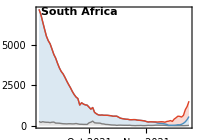

```mathematica
splitCasePlot["South Africa"]
```

```mathematica
panels=Map[splitCasePlot,countries];
```

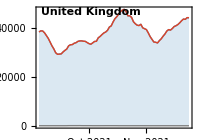
|  | 
-Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-cases.png

```mathematica
splitCaseLogPlot[country_]:=Module[{variantSeries},
variantSeries=Map[csVariantGather[country,#]&,variants];
DateListLogPlot[variantSeries,Frame->{True,True,False,False},FrameLabel->{"","Cases"},PlotTheme->"FullAxes",ImageSize->200,AspectRatio->0.7,ImagePadding->{{50,15},{15,10}},Joined->True,PlotRange->{Automatic,
{8,All}},PlotRangePadding->{{Scaled[0.01],Scaled[0.01]},{Scaled[0.01],Scaled[0.15]}},PlotStyle->colors,FrameTicks->{{{10,100,1000,10000},Automatic},{dateTicks,Automatic}},
Epilog->Text[Style[country,Black,FontSize->11,FontWeight->Bold,FontFamily->"Helvetica"],Scaled[{0.03,1}],{-1,1}]]
]
```

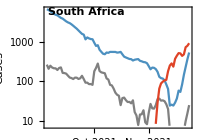

```mathematica
splitCaseLogPlot["South Africa"]
```

```mathematica
panels=Map[splitCaseLogPlot,countries];
```

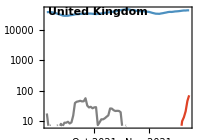
|  | 
-Graphics- | -Graphics- |

```mathematica
fig=Grid[gappedPartition[Join[{legendPanel,SpanFromLeft,SpanFromLeft},panels],3],Spacings->{0,0},Alignment->Right]
```

```mathematica
Export["figures/"<>dataset<>"_partitioned-log-cases.png",fig,"PNG",ImageResolution->300]
```

figures/omicron-countries_partitioned-log-cases.png